### [Part 3-10] Krylov state complexity

#### [Part 3-10-0] σ0 = 0

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
DATA=Import["STATIC_SIGMA0.dat"];
```

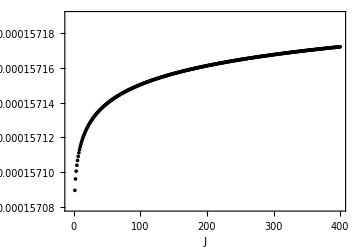

```mathematica
ListPlot[DATA,PlotStyle->Black,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->16},RotateLabel->False,Frame->True,FrameLabel->{"J","ω"},ImageSize->Medium,PlotRange->{{-5,400},{0.00015708,0.00015719}}]
```

```mathematica
EVa=DATA⟦All,2⟧;

HD=DiagonalMatrix[EVa];
Eβ2=Exp[-β/2 EVa];
Eβ=Exp[-β EVa];
Zβ=Plus@@Eβ;
Vnn[j_]:=Transpose[{Table[KroneckerDelta[j,i],{i,Length[EVa]}]}]
TFD[A_]:=1/(√Zβ)Sum[Eβ2[[k]]Vnn[k],{k,Length[EVa]}]/.β->A
W[A_]:=TFD[A]-Vnn[1]
```

```mathematica
EVa//Length
```

400

```mathematica
UR[A_]:=IdentityMatrix[Length[EVa]]-2/((Transpose[W[A]].W[A])[[1,1]])W[A].Transpose[W[A]]
HFin[A_]:=UR[A].HD.UR[A]
```

```mathematica
HFin[0];
{pF,hF}=HessenbergDecomposition[%];
HFG=Abs[hF-DiagonalMatrix[Diagonal[hF]]]+DiagonalMatrix[Diagonal[hF]];
ais=Diagonal[HFG];
bis=Join[{0},Table[HFG[[i,i+1]],{i,1,Length[HFG]-1}]];
Speak["Finish"]
```

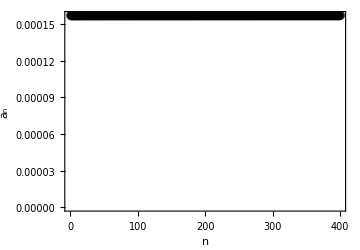
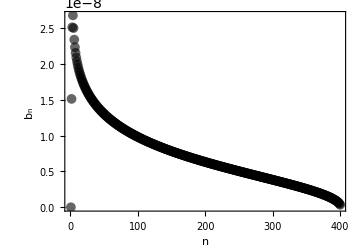

```mathematica
{ListPlot[ais,PlotMarkers->Style["●",10],PlotStyle->Opacity[0.6,Black],AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"n","a_n"},ImageSize->Medium,PlotRange->All],

ListPlot[bis,PlotMarkers->Style["●",10],PlotStyle->Opacity[0.6,Black],AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"n","b_n"},ImageSize->Medium,PlotRange->All]}
```

```mathematica
COMP[tn0_]:=
Module[{tn=tn0},
Clear[t,DEitH,VT,VTi,ExpHF,ProbF,KK];
t=tn;
DEitH=DiagonalMatrix[Exp[-ⅈ t Eigenvalues[HFG//N]]];
VT=Transpose[Eigenvectors[HFG//N]];
VTi=Inverse[VT];
ExpHF=VT.DEitH.VTi;

ProbF=Abs[ExpHF.Vnn[1]]^2//Flatten;
KK=Sum[(i-1) ProbF[[i]],{i,Length[ProbF]}]]
```

```mathematica
Dynamic[tn//N]
```

```mathematica
FINAL1 = Parallelize[Table[{tn,COMP[tn]},{tn,0,6*10^11,10^9}]];
Speak["Finish"]
```

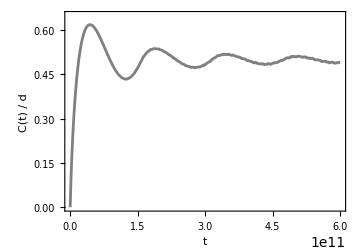

```mathematica
ListPlot[FINAL1/.{x_,y_}->{x,y/400},PlotStyle->{Gray(*Opacity[0.6,Red]*)},Joined->True,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C(t) / d"},ImageSize->Medium,PlotRange->{{0,6*10^11},{0,(*220*)0.65}}]
```

#### [Part 3-10-1] σ0 = 0.017

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
DATA=Import["STATIC_SIGMA0017.dat"];
```

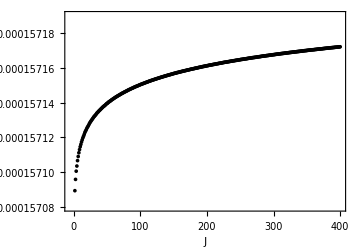

```mathematica
ListPlot[DATA,PlotStyle->Black,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->16},RotateLabel->False,Frame->True,FrameLabel->{"J","ω"},ImageSize->Medium,PlotRange->{{-5,400},{0.00015708,0.00015719}}]
```

```mathematica
EVa=DATA⟦All,2⟧;

HD=DiagonalMatrix[EVa];
Eβ2=Exp[-β/2 EVa];
Eβ=Exp[-β EVa];
Zβ=Plus@@Eβ;
Vnn[j_]:=Transpose[{Table[KroneckerDelta[j,i],{i,Length[EVa]}]}]
TFD[A_]:=1/(√Zβ)Sum[Eβ2[[k]]Vnn[k],{k,Length[EVa]}]/.β->A
W[A_]:=TFD[A]-Vnn[1]
```

```mathematica
EVa//Length
```

400

```mathematica
UR[A_]:=IdentityMatrix[Length[EVa]]-2/((Transpose[W[A]].W[A])[[1,1]])W[A].Transpose[W[A]]
HFin[A_]:=UR[A].HD.UR[A]
```

```mathematica
HFin[0];
{pF,hF}=HessenbergDecomposition[%];
HFG=Abs[hF-DiagonalMatrix[Diagonal[hF]]]+DiagonalMatrix[Diagonal[hF]];
ais=Diagonal[HFG];
bis=Join[{0},Table[HFG[[i,i+1]],{i,1,Length[HFG]-1}]];
Speak["Finish"]
```

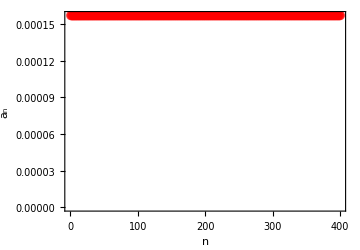
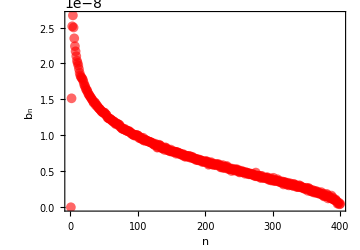

```mathematica
{ListPlot[ais,PlotMarkers->Style["●",10],PlotStyle->Opacity[0.6,Red],AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"n","a_n"},ImageSize->Medium,PlotRange->All],

ListPlot[bis,PlotMarkers->Style["●",10],PlotStyle->Opacity[0.6,Red],AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"n","b_n"},ImageSize->Medium,PlotRange->All]}
```

```mathematica
COMP[tn0_]:=
Module[{tn=tn0},
Clear[t,DEitH,VT,VTi,ExpHF,ProbF,KK];
t=tn;
DEitH=DiagonalMatrix[Exp[-ⅈ t Eigenvalues[HFG//N]]];
VT=Transpose[Eigenvectors[HFG//N]];
VTi=Inverse[VT];
ExpHF=VT.DEitH.VTi;

ProbF=Abs[ExpHF.Vnn[1]]^2//Flatten;
KK=Sum[(i-1) ProbF[[i]],{i,Length[ProbF]}]]
```

```mathematica
Dynamic[tn//N]
```

```mathematica
FINAL2 = Parallelize[Table[{tn,COMP[tn]},{tn,0,4*10^11,10^9}]];
Speak["Finish"]
```

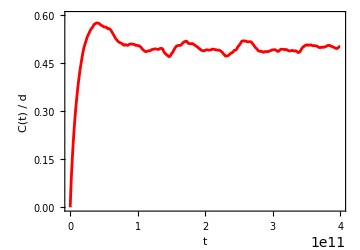

```mathematica
ListPlot[FINAL2/.{x_,y_}->{x,y/400},PlotStyle->{Red(*Opacity[0.6,Red]*)},Joined->True,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C(t) / d"},ImageSize->Medium,PlotRange->{{0,4*10^11},{0,(*220*)0.60}}]
```

```mathematica
DATA2 = DATA/.{x_,y_}->{x,y/400}//N;
```

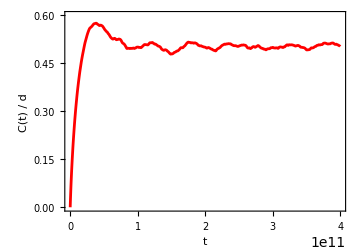

```mathematica
Plot[Interpolation[DATA2][t],{t,0,4*10^11},PlotStyle->{Red},AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C(t) / d"},ImageSize->Medium,PlotRange->{{0,4*10^11},{0,0.60}}]
```

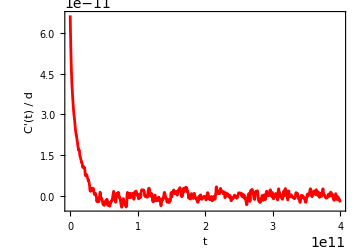

```mathematica
Plot[Interpolation[DATA2]'[t],{t,0,4*10^11},PlotStyle->{Red},AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C'(t) / d"},ImageSize->Medium,PlotRange->All]
```

#### [Part 3-10-2] σ0 = 0.024

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
DATA=Import["STATIC_SIGMA0024.dat"];
```

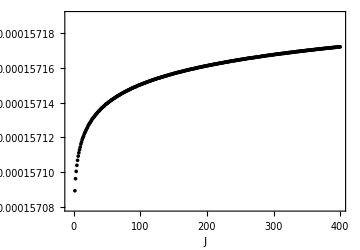

```mathematica
ListPlot[DATA,PlotStyle->Black,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->16},RotateLabel->False,Frame->True,FrameLabel->{"J","ω"},ImageSize->Medium,PlotRange->{{-5,400},{0.00015708,0.00015719}}]
```

```mathematica
EVa=DATA⟦All,2⟧;

HD=DiagonalMatrix[EVa];
Eβ2=Exp[-β/2 EVa];
Eβ=Exp[-β EVa];
Zβ=Plus@@Eβ;
Vnn[j_]:=Transpose[{Table[KroneckerDelta[j,i],{i,Length[EVa]}]}]
TFD[A_]:=1/(√Zβ)Sum[Eβ2[[k]]Vnn[k],{k,Length[EVa]}]/.β->A
W[A_]:=TFD[A]-Vnn[1]
```

```mathematica
EVa//Length
```

400

```mathematica
UR[A_]:=IdentityMatrix[Length[EVa]]-2/((Transpose[W[A]].W[A])[[1,1]])W[A].Transpose[W[A]]
HFin[A_]:=UR[A].HD.UR[A]
```

```mathematica
HFin[0];
{pF,hF}=HessenbergDecomposition[%];
HFG=Abs[hF-DiagonalMatrix[Diagonal[hF]]]+DiagonalMatrix[Diagonal[hF]];
ais=Diagonal[HFG];
bis=Join[{0},Table[HFG[[i,i+1]],{i,1,Length[HFG]-1}]];
Speak["Finish"]
```

```mathematica
Opacity[0.6,Darker[Green]]
```

Opacity[0.6,RGBColor[0, Rational[2, 3], 0]]

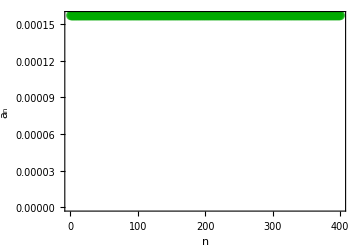
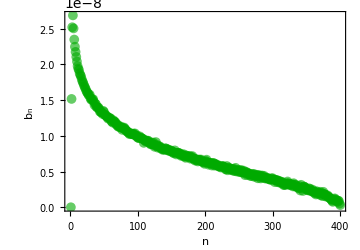

```mathematica
{ListPlot[ais,PlotMarkers->Style["●",10],PlotStyle->Opacity[0.6,Darker[Green]],AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"n","a_n"},ImageSize->Medium,PlotRange->All],

ListPlot[bis,PlotMarkers->Style["●",10],PlotStyle->Opacity[0.6,Darker[Green]],AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"n","b_n"},ImageSize->Medium,PlotRange->All]}
```

```mathematica
COMP[tn0_]:=
Module[{tn=tn0},
Clear[t,DEitH,VT,VTi,ExpHF,ProbF,KK];
t=tn;
DEitH=DiagonalMatrix[Exp[-ⅈ t Eigenvalues[HFG//N]]];
VT=Transpose[Eigenvectors[HFG//N]];
VTi=Inverse[VT];
ExpHF=VT.DEitH.VTi;

ProbF=Abs[ExpHF.Vnn[1]]^2//Flatten;
KK=Sum[(i-1) ProbF[[i]],{i,Length[ProbF]}]]
```

```mathematica
Dynamic[tn//N]
```

```mathematica
FINAL3 = Parallelize[Table[{tn,COMP[tn]},{tn,0,4*10^11,10^9}]];
Speak["Finish"]
```

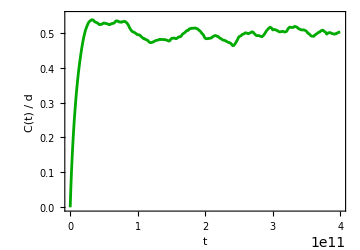

```mathematica
ListPlot[FINAL3/.{x_,y_}->{x,y/400},PlotStyle->{(*Opacity[0.6,Darker[Green]]*)Darker[Green]},Joined->True,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C(t) / d"},ImageSize->Medium,PlotRange->{{0,4*10^11},{0,(*220*)0.55}}]
```

#### [Part 3-10-3] σ0 = 0.030

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
DATA=Import["STATIC_SIGMA0030.dat"];
```

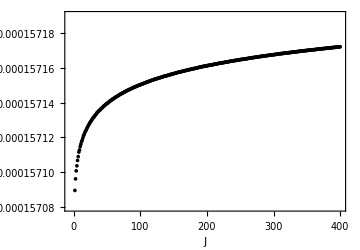

```mathematica
ListPlot[DATA,PlotStyle->Black,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->16},RotateLabel->False,Frame->True,FrameLabel->{"J","ω"},ImageSize->Medium,PlotRange->{{-5,400},{0.00015708,0.00015719}}]
```

```mathematica
EVa=DATA⟦All,2⟧;

HD=DiagonalMatrix[EVa];
Eβ2=Exp[-β/2 EVa];
Eβ=Exp[-β EVa];
Zβ=Plus@@Eβ;
Vnn[j_]:=Transpose[{Table[KroneckerDelta[j,i],{i,Length[EVa]}]}]
TFD[A_]:=1/(√Zβ)Sum[Eβ2[[k]]Vnn[k],{k,Length[EVa]}]/.β->A
W[A_]:=TFD[A]-Vnn[1]
```

```mathematica
EVa//Length
```

400

```mathematica
UR[A_]:=IdentityMatrix[Length[EVa]]-2/((Transpose[W[A]].W[A])[[1,1]])W[A].Transpose[W[A]]
HFin[A_]:=UR[A].HD.UR[A]
```

```mathematica
HFin[0];
{pF,hF}=HessenbergDecomposition[%];
HFG=Abs[hF-DiagonalMatrix[Diagonal[hF]]]+DiagonalMatrix[Diagonal[hF]];
ais=Diagonal[HFG];
bis=Join[{0},Table[HFG[[i,i+1]],{i,1,Length[HFG]-1}]];
Speak["Finish"]
```

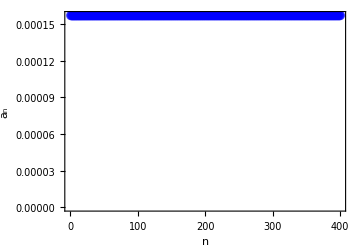
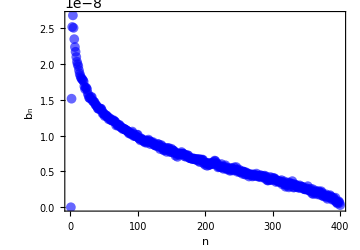

```mathematica
{ListPlot[ais,PlotMarkers->Style["●",10],PlotStyle->Opacity[0.6,Blue],AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"n","a_n"},ImageSize->Medium,PlotRange->All],

ListPlot[bis,PlotMarkers->Style["●",10],PlotStyle->Opacity[0.6,Blue],AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"n","b_n"},ImageSize->Medium,PlotRange->All]}
```

```mathematica
COMP[tn0_]:=
Module[{tn=tn0},
Clear[t,DEitH,VT,VTi,ExpHF,ProbF,KK];
t=tn;
DEitH=DiagonalMatrix[Exp[-ⅈ t Eigenvalues[Quiet[HFG//N]]]];
VT=Transpose[Eigenvectors[Quiet[HFG//N]]];
VTi=Inverse[VT];
ExpHF=VT.DEitH.VTi;

ProbF=Abs[ExpHF.Vnn[1]]^2//Flatten;
KK=Sum[(i-1) ProbF[[i]],{i,Length[ProbF]}]]
```

```mathematica
Dynamic[tn//N]
```

```mathematica
FINAL4 = Parallelize[Table[{tn,COMP[tn]},{tn,0,4*10^11,10^9}]];
Speak["Finish"]
```

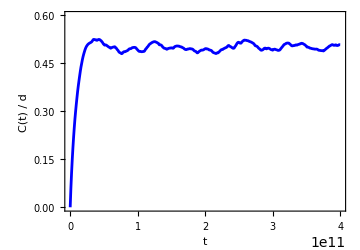

```mathematica
ListPlot[FINAL4/.{x_,y_}->{x,y/400},PlotStyle->{(*Opacity[0.6,Blue]*)Blue},Joined->True,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C(t) / d"},ImageSize->Medium,PlotRange->{{0,4*10^11},{0,(*220*)0.6}}]
```

#### [Part 3-10-4] σ0 = 0.5

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
DATA=Import["STATIC_SIGMA05.dat"];
```

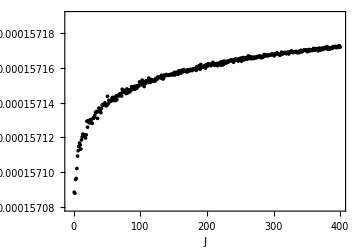

```mathematica
ListPlot[DATA,PlotStyle->Black,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->16},RotateLabel->False,Frame->True,FrameLabel->{"J","ω"},ImageSize->Medium,PlotRange->{{-5,400},{0.00015708,0.00015719}}]
```

```mathematica
EVa=DATA⟦All,2⟧;

HD=DiagonalMatrix[EVa];
Eβ2=Exp[-β/2 EVa];
Eβ=Exp[-β EVa];
Zβ=Plus@@Eβ;
Vnn[j_]:=Transpose[{Table[KroneckerDelta[j,i],{i,Length[EVa]}]}]
TFD[A_]:=1/(√Zβ)Sum[Eβ2[[k]]Vnn[k],{k,Length[EVa]}]/.β->A
W[A_]:=TFD[A]-Vnn[1]
```

```mathematica
EVa//Length
```

400

```mathematica
UR[A_]:=IdentityMatrix[Length[EVa]]-2/((Transpose[W[A]].W[A])[[1,1]])W[A].Transpose[W[A]]
HFin[A_]:=UR[A].HD.UR[A]
```

```mathematica
HFin[0];
{pF,hF}=HessenbergDecomposition[%];
HFG=Abs[hF-DiagonalMatrix[Diagonal[hF]]]+DiagonalMatrix[Diagonal[hF]];
ais=Diagonal[HFG];
bis=Join[{0},Table[HFG[[i,i+1]],{i,1,Length[HFG]-1}]];
Speak["Finish"]
```

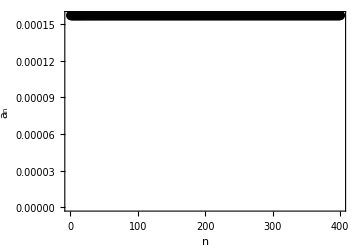
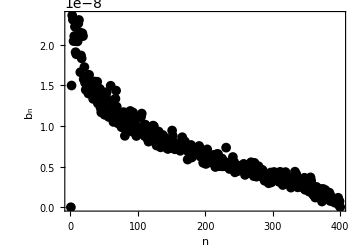

```mathematica
{ListPlot[ais,PlotMarkers->Style["●",10,Black],AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"n","a_n"},ImageSize->Medium,PlotRange->All],

ListPlot[bis,PlotMarkers->Style["●",10,Black],AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"n","b_n"},ImageSize->Medium,PlotRange->All]}
```

```mathematica
COMP[tn0_]:=
Module[{tn=tn0},
Clear[t,DEitH,VT,VTi,ExpHF,ProbF,KK];
t=tn;
DEitH=DiagonalMatrix[Exp[-ⅈ t Eigenvalues[HFG//N]]];
VT=Transpose[Eigenvectors[HFG//N]];
VTi=Inverse[VT];
ExpHF=VT.DEitH.VTi;

ProbF=Abs[ExpHF.Vnn[1]]^2//Flatten;
KK=Sum[(i-1) ProbF[[i]],{i,Length[ProbF]}]]
```

```mathematica
Dynamic[tn//N]
```

```mathematica
FINAL5 = Table[{tn,COMP[tn]},{tn,0,4*10^11,10^9}];
Speak["Finish"]
```

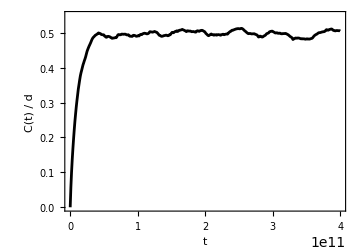

```mathematica
ListPlot[FINAL5/.{x_,y_}->{x,y/400},PlotStyle->{Black},Joined->True,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C(t) / d"},ImageSize->Medium,PlotRange->{{0,4*10^11},{0,(*220*)0.55}}]
```

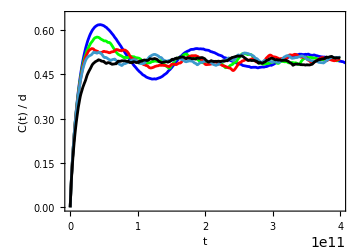

```mathematica
Show[{ListPlot[FINAL1/.{x_,y_}->{x,y/400},PlotStyle->{Blue},Joined->True,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C(t) / d"},ImageSize->Medium,PlotRange->{{0,4*10^11},{0,(*220*)0.65}}],ListPlot[FINAL2/.{x_,y_}->{x,y/400},PlotStyle->{Green},Joined->True,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C(t) / d"},ImageSize->Medium,PlotRange->{{0,4*10^11},{0,(*220*)0.65}}],ListPlot[FINAL3/.{x_,y_}->{x,y/400},PlotStyle->{Red},Joined->True,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C(t) / d"},ImageSize->Medium,PlotRange->{{0,4*10^11},{0,(*220*)0.65}}],ListPlot[FINAL4/.{x_,y_}->{x,y/400},PlotStyle->{Grey},Joined->True,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C(t) / d"},ImageSize->Medium,PlotRange->{{0,4*10^11},{0,(*220*)0.65}}],ListPlot[FINAL5/.{x_,y_}->{x,y/400},PlotStyle->{Black},Joined->True,AxesOrigin->{0,0},AspectRatio->7/10,LabelStyle-> {FontSize->15},RotateLabel->False,Frame->True,FrameLabel->{"t","C(t) / d"},ImageSize->Medium,PlotRange->{{0,4*10^11},{0,(*220*)0.65}}]}]
```

```mathematica
Export["KRYLOV_STATIC0.dat",FINAL1/.{x_,y_}->{x,y/400}]
Export["KRYLOV_STATIC0017.dat",FINAL2/.{x_,y_}->{x,y/400}]
Export["KRYLOV_STATIC0024.dat",FINAL3/.{x_,y_}->{x,y/400}]
Export["KRYLOV_STATIC0030.dat",FINAL4/.{x_,y_}->{x,y/400}]
Export["KRYLOV_STATIC05.dat",FINAL5/.{x_,y_}->{x,y/400}]
```

KRYLOV_STATIC0.dat

KRYLOV_STATIC0017.dat

KRYLOV_STATIC0024.dat

KRYLOV_STATIC0030.dat

KRYLOV_STATIC05.dat